## 6.859 A4: Does Charlie WFH?

## Georgios Varnavides, Max L’Etoille

## MBTA Rapid Transit Shape Files

### Raw Data

```mathematica
SetDirectory[FileNameDrop[NotebookDirectory[],-2]]
```

/home/george/Documents/git-repos/a4-does-charlie-wfh

```mathematica
Keys[shapeFilesAssociations=With[{fileName="data/mbta_rapid_transit.zip"},
Association/@AssociationThread[Import[fileName,"LayerNames"]->Import[fileName,"Data"]]]]
geometryAssociations=Map[#["Geometry"]/. {Line[x_]:>(Line[GeoGridPosition[#,"SPCS83MA01"]&/@x]),Point[x_]:>Point[GeoGridPosition[x,"SPCS83MA01"]]}&,shapeFilesAssociations];
```

{MBTA_ARC,MBTA_NODE}

### Grouping By Lines

```mathematica
cols={Blue,RGBColor[0,1/3,0],Orange,Red,Interpreter["Color"]["#C0C0C0"]}
```

{RGBColor[0, 0, 1],RGBColor[0, Rational[1, 3], 0],RGBColor[1, 0.5, 0],RGBColor[1, 0, 0],RGBColor[Rational[64, 85], Rational[64, 85], Rational[64, 85]]}

```mathematica
groupedRoutesByLine=KeySort[With[{lineMetaData=Association[shapeFilesAssociations["MBTA_ARC","LabeledData"]]["LINE"]},
GroupBy[Thread[{Range[Length[lineMetaData]],lineMetaData}],Last][[All,All,1]]]];
```

```mathematica
splitSharedStations[key_,value_]:=Block[{stations},
stations=StringSplit[key,"/"];
<|stations[[1]]->value,stations[[2]]->value|>]

groupedStationsByLineTmp=KeySort[With[{lineMetaData=Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]]["LINE"]},
GroupBy[Thread[{Range[Length[lineMetaData]],lineMetaData}],Last][[All,All,1]]]];
sharedStationsAsc=KeySelect[groupedStationsByLineTmp,StringContainsQ["/"]];
groupedStationsByLine=KeySort[KeyDrop[Flatten/@Merge[{groupedStationsByLineTmp,Flatten/@Merge[KeyValueMap[splitSharedStations,sharedStationsAsc],Identity]},Identity],Keys[sharedStationsAsc]]];
```

```mathematica
GeoGraphics[{
MapThread[{Thick,#1,geometryAssociations["MBTA_ARC"][[groupedRoutesByLine[#2]]]}&,{cols,groupedRoutesByLine//Keys}],MapThread[{PointSize[Large],#1,geometryAssociations["MBTA_NODE"][[groupedStationsByLine[#2]]]}&,{cols,groupedStationsByLine//Keys}]},GeoBackground->"VectorDark"]//Rasterize
```

-Graphics-

### Cleaning up

First, we drop the Silver line

It’s bus-operated

Most of its stations don’t/can’t record gate validations

A lot of its traffic is airport-related, so unlikely to be representative of housing prices and commutes

```mathematica
cleanedUpRoutesByLine=KeySort@KeyDrop[groupedRoutesByLine,"SILVER"];
cleanedUpCols=Most[cols]
```

{RGBColor[0, 0, 1],RGBColor[0, Rational[1, 3], 0],RGBColor[1, 0.5, 0],RGBColor[1, 0, 0]}

Second, we ‘bin’ stations w/ multiple entrances to one GeoPosition

Turns out there’s only one such pair once we remove the silver line nodes

St. Paul St on GL-C with two locations ~0.5 mile apart

We pick the one on Comm Ave

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```

```mathematica
Select[DeleteCases[#,Alternatives@@groupedStationsByLine["SILVER"]]&/@positionDuplicates[Lookup[Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]],"STATION"]],Length[#]>1&]
Lookup[Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]],"STATION"][[First[%]]]
GeoDistance@@GeoPosition/@geometryAssociations["MBTA_NODE"][[First[%%],1]]
```

{{82,105}}

{Saint Paul Street,Saint Paul Street}

0.550605 mi

```mathematica
cleanedUpStations=Delete[Transpose[Append[Lookup[Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]],{"STATION","LINE"}],GeoPosition/@geometryAssociations["MBTA_NODE"][[All,1]]]],List/@Append[groupedStationsByLine["SILVER"],105]];

splitSharedStationsClean[row_]:=If[StringContainsQ["/"][row[[2]]],
Table[{row[[1]],station,row[[3]]},{station,StringSplit[row[[2]],"/"]}],{row}]

cleanedUpStations=SortBy[Flatten[splitSharedStationsClean/@cleanedUpStations,1],#[[2]]&];
cleanedUpStationsByLine=KeySort[GroupBy[cleanedUpStations,#[[2]]&]];
```

Visually Debugging

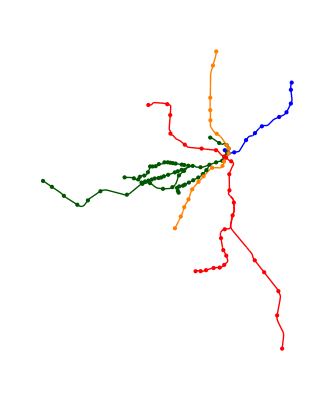

```mathematica
GeoGraphics[{
MapThread[{Thick,#1,geometryAssociations["MBTA_ARC"][[cleanedUpRoutesByLine[#2]]]}&,{cleanedUpCols,cleanedUpRoutesByLine//Keys}],MapThread[{PointSize[Large],#1,Point[cleanedUpStationsByLine[#2][[All,3]]]}&,{cleanedUpCols,cleanedUpStationsByLine//Keys}]},GeoBackground->None]
```

### Exporting Clean Datasets

CSV of stations only for now

we'll see what the best format for the GeoGraphics is down the line

The table below deliberately has ‘duplicate station entries’

E.g. Park Street station has a row entry for both RED and GREEN lines

```mathematica
cleanedUpStationsDataset=Prepend[Flatten/@MapAt[First,cleanedUpStations,{All,3}][[All,{2,1,3}]],{"LINE","STATION NAME","LATITUDE","LONGITUDE"}];
```

```mathematica
Export["data/mbta_rapid_transit_stations.csv",cleanedUpStationsDataset,"CSV"]
```

data/mbta_rapid_transit_stations.csv